# Field quantization

Install and load the Quantum Framework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
```

```mathematica
Needs["Wolfram`QuantumFramework`"]
```

## Quantization of a single mode field

Let’s start with the simple case of a 1D cavity  along the z axis with perfectly conducting walls at z = 0 and z = L. Assuming the electric field is polarized in the x direction E(r,t) =  e_x E_x (z,t) where e_x is a unit vector along x, we also assume there are no sources of radiation (charges, currents, etc).

Maxwell equations without sources in SI units:




A single mode field  that satisfy the equations with the boundary conditions:

Where ω is the mode frequency , k is the wave number and V is the effective cavity volume . The boundary conditions allow  ω_m = c (m π / L), m = 1,2,...

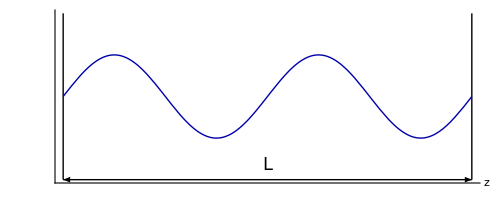

```mathematica
Show[{Graphics[{Line[{{0,-2},{0,2}}],Line[{{4Pi,-2},{4Pi,2}}],Arrowheads[{-.05,.05}],Arrow[{{0,-2},{4Pi,-2}}],Text[Style["L",18],{2Pi,-1.65}]}],Plot[Sin[x],{x,0,4Pi},PlotStyle->Directive[Darker[Blue],Thick]]},Axes->True,Ticks->None, AxesLabel->{"z",""}]
```

In a similar way the magnetic field in the cavity is B(r , t) = e_y B_y(z, t) where:
 
q(t)  is a time dependent function that represents canonical position and  q̇(t) = p(t) represents canonical momentum with unit mass.
The energy of the field that coincides with  Hamiltonian H is
 
It can be shown  that is equivalent to an harmonic oscillator of unit mass, where p and q  are canonical momentum and position up to scaling factors

Quantizing the harmonic oscillator of unit mass promotes the canonical variables p and q to operators p̂ and q̂ that satisfy the commutation relation

So the Hamiltonian becomes:

It is standard to introduce  non Hermitian(non observable) operators â and (â)^† which have more significance than just for sake of algebraic manipulation


Electric and magnetic field become


Where  ℰ_0 = (ℏ ω / ϵ_0 V)^(1/2) and ℬ_0 = (μ_0/k)(ϵ_0 ℏ ω^3/V)^(1/2) can be interpreted as electric and magnetic fields per photon. However, this is not really correct , because we will show a quantum state with a definite number of photons has expectation value of zero of these operators.

The â and (â)^† operators follow the commutation relation  and as a result ,   is called the number operator . Considering  |n⟩  an energy eigenstate then the eigenvalue equation  is
 
With energy eigenvalues:
 

-Graphics-

The creation and annihilation operator raises (or lower) a state to another state with an energy increase (or decrease) of  ℏω , that is why they are said to be bosonic operators that create or annihilate a photon

## Definitions

Creation and annihilation operator of size n:

```mathematica
creationAnnihilation[n_]:=Module[{ca,aa},
aa=QuantumOperator[Table[If[i==j+1,Sqrt[i-1],0],{i,1,n},{j,1,n}],n];
ca=aa["Dagger"];
{ca,aa}]
```

Particular nth Fock state in a basis of size d:

```mathematica
fockN[n_,d_]:= QuantumState[SparseArray[{n+1 -> 1}, d], d]
```

## Basic properties of creation and annihilation operators

We can specify the size of  the Fock space

```mathematica
size = 11;
```

```mathematica
{a,a†} = creationAnnihilation[size];
```

```mathematica
fockBasis = a["OutputBasis"]
```

<|0→{1,0,0,0,0,0,0,0,0,0,0},1→{0,1,0,0,0,0,0,0,0,0,0},2→{0,0,1,0,0,0,0,0,0,0,0},3→{0,0,0,1,0,0,0,0,0,0,0},4→{0,0,0,0,1,0,0,0,0,0,0},5→{0,0,0,0,0,1,0,0,0,0,0},6→{0,0,0,0,0,0,1,0,0,0,0},7→{0,0,0,0,0,0,0,1,0,0,0},8→{0,0,0,0,0,0,0,0,1,0,0},9→{0,0,0,0,0,0,0,0,0,1,0},10→{0,0,0,0,0,0,0,0,0,0,1}|>

Creation  and  annihilation are  non Hermitian operators with commutator

```mathematica
a @ fockN[5,size]
```

√5 4

```mathematica
a† @ fockN[5,size]
```

√6 6

Nested application of the annihilation  operator eventually makes any number state goes to the vacuum , and one more application returns the scalar zero:

```mathematica
NestList[a,fockN[size-1,size],size]
```

{10,√10 9,3 √108,12 √57,12 √356,12 √2105,60 √424,120 √423,360 √142,720 √71,720 √70,0}

It is possible to  build  nth Fock state from vacuum |n⟩ = ((a^†)^n)/(√(n!))|0⟩:

```mathematica
Nest[a†,QuantumState["0",size],5]/√Factorial[5]
```

5

Photon number operator (observable) :

```mathematica
numberOp =a†@a
```

11+222+333+444+555+666+777+888+999+101010

```mathematica
st = QuantumState[1/Sqrt[2]SparseArray[{3->1,8->1},10],fockBasis]
```

1/(√2)2+1/(√2)7

Mean number of photons using QuantumMeasurementOperator and alternative approach:

```mathematica
(QuantumMeasurementOperator[numberOp]@st)["Mean"]//AbsoluteTiming
```

{0.30062,9/2}

```mathematica
KeyValueMap[#1[[1]] #2 &, st["Probability"]]//Total //AbsoluteTiming
```

{0.0008396,9/2}

## Quantum fluctuations for a single mode field

The energy eigenstate |n⟩ has well defined energy but does not have a well defined electric field because
⟨ n |E_x( z,t)|n ⟩ =  ℰ_0 sin(k z)[ ⟨n|a|n⟩ + ⟨ n|a^†| n⟩ ] =  0

```mathematica
fieldOp = Subscript[ℰ, 0] Sin[k z](a+a†);
```

```mathematica
(#["Dagger"]@fieldOp @ #)["Scalar"]& /@ Table[fockN[n,size],{n,0,size-1}]
```

{0,0,0,0,0,0,0,0,0,0,0}

However, the electric field squared is not zero:
⟨ n |E_x^2( z,t)|n ⟩ =  (ℰ^2)_0 sin^2(k z)[ ⟨n|(a^†)^2 +a^2+a^†a + a a^†|n⟩] =  (ℰ^2)_0 sin^2(k z) ⟨n|(a^†)^2 +a^2+2 a^†a + 1|n⟩] = (ℰ^2)_0 sin^2(k z) (2  n + 1)

```mathematica
(#["Dagger"]@fieldOp@fieldOp @ #)["Scalar"]& /@ Table[fockN[n,size],{n,0,size-2}]
```

{Sin[k z]^2 ℰ_0^2,3 Sin[k z]^2 ℰ_0^2,5 Sin[k z]^2 ℰ_0^2,7 Sin[k z]^2 ℰ_0^2,9 Sin[k z]^2 ℰ_0^2,11 Sin[k z]^2 ℰ_0^2,13 Sin[k z]^2 ℰ_0^2,15 Sin[k z]^2 ℰ_0^2,17 Sin[k z]^2 ℰ_0^2,19 Sin[k z]^2 ℰ_0^2}

For an operator the variance is defined as and the standard deviation or uncertainty is the square root of the variance so for a number state we have :
ΔE_x = √2 ℰ_0 sin(k z) √(n + 1/2)    even when n = 0 the mean field is zero  but has non zero uncertainty , this phenomenon is called vacuum fluctuations. So a state with definite number of photons has zero  average field . This is related to uncertainty principle because n̂ and OverHat[E_x] do not commute [n, E_x] = ℰ_0 sin(k z) (a^†-a), the operators are complementary

## Quadrature operators of a single mode field

We define helper functions for the commutator and operator variance:

```mathematica
commutator[a_QuantumOperator,b_QuantumOperator]:=a@b - b@a 
operatorVariance[state_QuantumState, op_QuantumOperator]:= (state["Dagger"]@ (op @ op)@ state)["Scalar"] - (state["Dagger"]@ op @ state)["Scalar"]^2
```

```mathematica
setFockSize[40]
```

```mathematica
X1 = 1/2(a+a["Dagger"]);
```

```mathematica
X2 = 1/(2I)(a-a["Dagger"]);
```

,   but there is an error in the last term because of truncation

```mathematica
commutator[X1,X2]["Matrix"]//Diagonal //Normal
```

{ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,ⅈ/2,-(39 ⅈ)/2}

For a fock state , the ground state |0⟩attains the minimum value  1/4

```mathematica
With[{fockstates = fockBasis["BasisStates"][[1;;10]]},Table[{operatorVariance[ fockstate,X1],operatorVariance[ fockstate,X2]},{fockstate,fockstates}]]
```

{{1/4,1/4},{3/4,3/4},{5/4,5/4},{7/4,7/4},{9/4,9/4},{11/4,11/4},{13/4,13/4},{15/4,15/4},{17/4,17/4},{19/4,19/4}}

## Thermal fields

Considering  a single mode field in thermal equilibrium in a cavity at temperature T. From statistical mechanics the probability distribution  P_n that the n-th level is excited is:

where k_B is the Boltzmann constant

Using  the Hamiltonian  a mixed state described by a thermal density operator is defined based on the energy probability distribution:

The denominator is the partition function

```mathematica
En = h ω (n + 1/2);
```

The partition function Z is obtained:

```mathematica
Z =Sum[Exp[-En/(kb T)],{n,0,∞}]
```

ⅇ^((h ω)/(2 kb T))/(-1+ⅇ^((h ω)/(kb T)))

The probability distribution of having a state that has n photons is:

The average photon number is :

```mathematica
Sum[n Exp[-En/(kb T)],{n,0,∞}]/Z
```

1/(-1+ⅇ^((h ω)/(kb T)))

ρ_Th can be written in terms of n^— as:

```mathematica
thermalState[nbar_, size_]:=QuantumOperator[DiagonalMatrix [1/(1+nbar) Table[(nbar/(1+nbar))^n,{n,0,size}]],size+1]["MatrixQuantumState"]
```

```mathematica
thermalState[2.,39];
```

```mathematica
% // Tr
```

1.

Thermal field photon distribution varying the n^— parameter of the thermal state density matrix:

```mathematica
Manipulate[thermalState[nmean,fockBasis["Dimension"]-1]["ProbabilityPlot",PlotRange->{{-1,11.5},{0,1}},PlotRangePadding->0.09],{{nmean,0.1,"n^—"},0.1,2.,0.1},SaveDefinitions->True]
```

## The quantum phase

There have been many attempts to provide an accurate quantum description of the phase, Dirac tried to decompose creation and annihilation operators in polar form assuming an Hermitian operator ϕ exists. However, it can proved exp( ⅈ ϕ̂) cannot be unitary hence ϕ̂ cannot be Hermitian, Barnett and Pegg shown how to build unitary operators of the form e^(ⅈ ϕ̂) including non physical negative Fock states which do not really  add any new predictions. Other issues come from the fact ϕ̂ must be an angle operator and can be shown that can lead to problematic relations when angular momentum is considered.

We will follow a formalism introduced by Susskind and Glogover, where a kind of exponential phase operator is defined and their eigenstates “phase eigenstates” serve to build a phase distribution ; and expectation values can be calculated over the phase distribution. This approach is cleaner in the calculations and can provide insight about the phase behavior of a quantum state. 
The  Susskind-Glogower operators are defined by:

```mathematica
((a†@a+QuantumOperator["I"[11]])^(-1/2))@a
```

01+12+23+34+45+56+67+78+89+910

```mathematica
Ephase := QuantumOperator[DiagonalMatrix[Table[1,a["OutputDimension"]-1],1],a["OutputDimension"]]
```

Equivalent expression for the operators are:

Ê(Ê)^† = 1   and   (Ê)^†Ê =1-|0⟩⟨0|  ( in each case we get N -1 terms where N is the truncated space dimensionality)

```mathematica
Ephase@Ephase["Dagger"]
```

00+11+22+33+44+55+66+77+88+99

```mathematica
Ephase["Dagger"]@Ephase
```

11+22+33+44+55+66+77+88+99+1010

Ê and (Ê)^† themselves are not observables but the operators
Ĉ = 1/2(Ê+(Ê)^†)       and     Ŝ = 1/(2 ⅈ)(Ê-(Ê)^†)  represent  analogs of cos(ϕ) and sin(ϕ)

```mathematica
Cphase = 1/2(Ephase+Ephase["Dagger"])
Sphase = 1/(2ⅈ)(Ephase -Ephase["Dagger"])
```

```mathematica
commutator[a_QuantumOperator,b_QuantumOperator]:= a@b-b@a
```

Those operators are Hermitian and have commutator [Ĉ,Ŝ] = ⅈ/2 |0⟩⟨0| (in a truncated basis this commutator has error in the last term)

```mathematica
commutator[Cphase,Sphase]
```

ⅈ/2 00-ⅈ/21010

The known trigonometric Pythagorean identity has a close analog with a difference in the vacuum
(Ĉ)^2+(Ŝ)^2 =1-1/2|0⟩⟨0| ( there is also error in the last term due to truncation)

```mathematica
Cphase@Cphase + Sphase@Sphase
```

1/2 00+11+22+33+44+55+66+77+88+99+1/2 1010

The following commutators can be shown, that can be used to establish uncertainty relations:
[Ĉ,n̂] =ⅈ Ŝ    [Ŝ,n̂] = -ⅈ Ĉ

```mathematica
commutator[Cphase,a†@a] == ⅈ Sphase
```

True

```mathematica
commutator[Sphase,a†@a]== -ⅈ Cphase
```

True

For number states |n⟩  Δn = 0,  ⟨ n | Ĉ | n ⟩ = 0 and ⟨ n | Ŝ | n ⟩ =0

Then for n≥ 1   ΔC =ΔS  = 1/√2

```mathematica
Table[(fockN[n,11]["Dagger"]@Sphase@Sphase@fockN[n,11])["Scalar"],{n,0,9}]
```

{1/4,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

```mathematica
Table[(fockN[n,11]["Dagger"]@Cphase@Cphase@fockN[n,11])["Scalar"],{n,0,9}]
```

{1/4,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2,1/2}

The eigenstates |ϕ⟩ of the exponential operator hold the eigenvalue relation:
  are defined by

```mathematica
phistate := QuantumState[Table[ⅇ^(ⅈ n ϕ),{n,0,a["OutputDimension"]-1}],a["OutputDimension"],"Parameters"->ϕ]
```

As expected due to how Ê acts on Fock states, the last term fails in the eigenstate relation in a truncated space:

```mathematica
(Ephase @ phistate) == ⅇ^(ⅈ ϕ) phistate
```

{True,True,True,True,True,True,True,True,True,True,0==ⅇ^(10 ⅈ ϕ)}

Phase eigenstates resolve to unity  1/(2π)(∫_0)^(2π) |ϕ⟩ ⟨ϕ|ⅆϕ = 1

```mathematica
phiProj =FullSimplify[QuantumOperator[phistate @phistate["Dagger"],a["OutputDimension"]],Element[ϕ,Reals]];
```

```mathematica
QuantumOperator[1/(2π)Integrate[phiProj["Matrix"],{ϕ,0,2π}],a["OutputDimension"]]
```

00+11+22+33+44+55+66+77+88+99+1010

A phase distribution 𝒫(ϕ) can be calculated for the state |ψ⟩ with the calculation recipe:
𝒫(ϕ) = 1/2π  | ⟨ϕ | ψ⟩|^2
this distribution can be used to calculate average values for functions of ϕ
⟨ f(ϕ) ⟩ = ∫_0^(2π) f(ϕ)𝒫(ϕ)ⅆϕ

For any number state |n⟩ the phase distribution is 𝒫(ϕ) = 1/2π  which is a uniform distribution which has mean π and fluctuations Δϕ = π/√3, this holds for all states including vacuum

```mathematica
Table[1/(2π)Abs[(phistate["Dagger"]@fockN[n,11])["Scalar"]]^2//Simplify[#,ϕ∈Reals]&,{n,0,a["OutputDimension"]-1}]
```

{1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π),1/(2 π)}

```mathematica
{Mean[UniformDistribution[{0,2π}]],StandardDeviation[UniformDistribution[{0,2π}]]}
```

{π,π/(√3)}

There exist other approaches to the quantum phase, but this approach is supported by quantum estimation theory and generates a probability operator that measures maximum likelihood phase estimation. Given that is not trivial to claim there is a single correct phase operator, SG operators offer at least qualitatively a reasonable description of a quantum phase variable